```mathematica
1+1
```

2

```mathematica
Integrate[f'[x]g[x]+g'[x]f[x],x]
```

f[x] g[x]

```mathematica
Integrate[f'[x]g[x],x]+Integrate[f[x]g'[x],x]==a[x]+Integrate[f[x]g'[x],x]
```

∫g[x] f'[x]ⅆx+∫f[x] g'[x]ⅆx==a[x]+∫f[x] g'[x]ⅆx

```mathematica
FullSimplify[Integrate[f'[x]g[x],x]+Integrate[f[x]g'[x],x]==a[x]+Integrate[f[x]g'[x],x],x∈Reals]
```

a[x]==∫g[x] f'[x]ⅆx

```mathematica
Integrate[f'[x]g[x]+f[x]g'[x],x]==a[x]+Integrate[f[x]g'[x],x]
```

f[x] g[x]==a[x]+∫f[x] g'[x]ⅆx

```mathematica
D[x^2 x,x]
```

3 x^2

```mathematica
2x x+x^2
```

3 x^2

```mathematica
Sin[x]Sin'[x]+Sin[x]Sin'[x]
```

2 Cos[x] Sin[x]

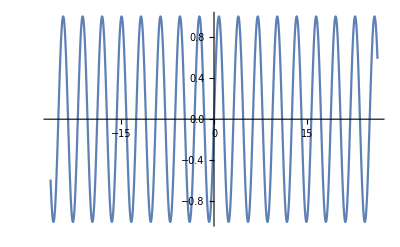

```mathematica
Plot[2 Cos[x] Sin[x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Sin[x]Sin'[x]
```

Cos[x] Sin[x]

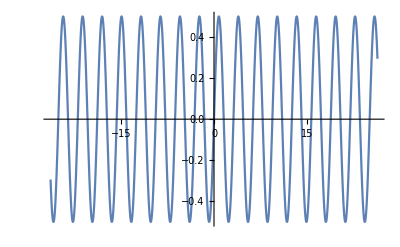

```mathematica
Plot[Cos[x] Sin[x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
f[x] g[x]-∫f[x] g'[x]ⅆx==a[x]
```

f[x] g[x]-∫f[x] g'[x]ⅆx==a[x]

```mathematica
Integrate[Sin[x]Sin'[x],x]
```

-1/2 Cos[x]^2

```mathematica
With[{f=Sin,g=Sin},f[x] g[x]-∫f[x] g'[x]ⅆx==a[x]]
```

Cos[x]^2/2+Sin[x]^2==a[x]

```mathematica
D[f[x]g[x],x]
```

g[x] f'[x]+f[x] g'[x]

```mathematica
∫(g[x] f'[x]+f[x] g'[x])ⅆx
```

f[x] g[x]

```mathematica
Integrate[f'[x]g[x],x]==Integrate[a'[x],x]
```

∫g[x] f'[x]ⅆx==a[x]

```mathematica
∫g[x] f'[x]ⅆx+∫g'[x] f[x]ⅆx==a[x]+∫g'[x] f[x]ⅆx
```

∫g[x] f'[x]ⅆx+∫f[x] g'[x]ⅆx==a[x]+∫f[x] g'[x]ⅆx

```mathematica
∫g[x] f'[x]+f[x] g'[x]ⅆx==a[x]+∫f[x] g'[x]ⅆx
```

Integrate::nodiffd: ∫g[x]f'[x] cannot be interpreted. Integrals are entered in the form ∫fⅆx, ∫_a^b , or ∫_(vars ∈ region) , where ⅆ is entered as EscddEsc.

```mathematica
∫(g[x] f'[x]+f[x] g'[x])ⅆx==a[x]+∫f[x] g'[x]ⅆx
```

f[x] g[x]==a[x]+∫f[x] g'[x]ⅆx

```mathematica
f[x] g[x]-∫f[x] g'[x]ⅆx==a[x]
```

f[x] g[x]-∫f[x] g'[x]ⅆx==a[x]

```mathematica
∫g[x] f'[x]ⅆx
```

∫g[x] f'[x]ⅆx

```mathematica
∫(g[x] f'[x]+g'[x]f[x])ⅆx
```

f[x] g[x]

```mathematica
∫(f'[g[x]]g'[x])ⅆx
```

f[g[x]]

```mathematica
Dt[f[g[x]]]
```

Dt[x] f'[g[x]] g'[x]

```mathematica
(Dt[x] f'[g[x]] g'[x])/Dt[x]
```

f'[g[x]] g'[x]

```mathematica
0^0
```

Power::indet: Indeterminate expression 0^0 encountered.

Indeterminate

```mathematica
∞ 0
```

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Indeterminate

```mathematica
∞/0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
∞/∞
```

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Indeterminate

```mathematica
∞ ∞
```

∞

```mathematica
FullForm[∞]
```

DirectedInfinity[1]

```mathematica
TraditionalForm[Inactivate[Integrate[f'[x],x]g[x]-∫f[x] g'[x]ⅆx==a[x]]]
```

Derivative[1][f][x]x*g[x]+-1*f[x]*Derivative[1][g][x]x==a[x]

```mathematica
TraditionalForm[Hold[Integrate[f'[x],x]g[x]-∫f[x] g'[x]ⅆx==a[x]]]
```

Hold[g(x) (∫f'(x)ⅆx)-∫f(x) g'(x)ⅆx==a(x)]